```mathematica
(*1.grf comstructiom*)
distribution=TransformedDistribution[r Exp[0*I t],{r\[Distributed]NormalDistribution[0 ,1],t\[Distributed]UniformDistribution[{0,2 Pi}]}]; 
grfreset:=Module[{},inpoints={};
inval={};
];
corr[x_]=Exp[-x^2];
grf[newpoint_,lh2_,lv2_]:=Module[{val},
dim=Length[newpoint];
lh=lh2; (*Horizontal scale*)
lv=lv2; (*Vertical scale*)
val=lv*evaluateat[newpoint*1/lh];val];
evaluateat[newpoint_]:=Module[{len,val,check},
{len=Length[inpoints];
If[len==0,{
inpoints={newpoint};
val=RandomVariate[distribution];
inval={val};},

{check=Position[inpoints,newpoint];

If[Length[check]==0,
val=grfadd[newpoint];
If[checkit==0,
{inval=Append[inval,val];
inpoints=Append[inpoints,newpoint];}
];,
{
val=inval[[check[[1,1]]]];}
];
}];
val}
][[1]];
grfadd[newpoint_]:=Module[{len},
len=Length[inpoints];
c0=1;
normm=Sqrt[Total[Abs[Transpose[Transpose[inpoints]-newpoint]]^2,{2}]];
boole=Boole[Negative[normm-5]];(*selects all points from inpoints that are within 5 correlation lengths of the newpoint*)
sel=Flatten[Position[boole,1]];
sellen=Length[sel];

	If[sellen==0,
		{a=RandomVariate[distribution]},
		{invalsel=Table[inval[[ii]],{ii,sel}];
		inpointssel=Table[inpoints[[ii]],{ii,sel}];
		m3=Table[0,{sellen},{sellen}];
		Table[{inplast=inpointssel[[i]] ;
			normm2=Sqrt[Total[Abs[Transpose[Transpose[Take[inpointssel,i]]-inplast]]^2,{2}]];
			normm2=Take[normm2,i-1];
			m3[[i,1;;i-1]]=normm2;
			m3[[1;;i-1,i]]=normm2;
			}
		,{i,2,sellen}];
		csel=corr[m3];
		cjsel=corr[normm[[sel]]];
		fasel=Quiet[LinearSolve[csel,cjsel]];
		fa22sel=1-cjsel.fasel;
		fa2sel=Sqrt[fa22sel];		
		pre=Norm[csel.fasel-cjsel];
		If[Or[pre>10^-12,fa22sel/Norm[fasel]<10^-6],
		{checkit=1;
			fa2sel=0;},checkit=0
		];
a=fa2sel*RandomVariate[distribution]+fasel.invalsel;
}
];
a
];
```

```mathematica
(*2.inflation parameter set*)
φstep=0.05;
m=10^-6;
amp=10^-15;
φmax=30;
φstart=φmax-φstep;
Δt=10^5;
steps=500;
η:=RandomReal[NormalDistribution[0,1/√Δt]];
V0[x1_,x2_]:=1/2 m^2 x1^2;
VR=Table[0,{i,steps}];
VR1=Table[0,{i,steps}];
VR2=Table[0,{i,steps}];
VTOTAL=Table[0,{i,steps}];
H=Table[0,{i,steps}];
```

```mathematica
(*3.inflation trajectory*)
φ1=Table[0,{i,steps}];
φ2=Table[0,{i,steps}];
φ1[[1]]=φstart;
φ2[[1]]=φmax/2;
grfreset[];
VR[[1]]=grf[{φ1[[1]],φ2[[1]]},φstep,amp];
Module[{plus1,plus2},plus1=grf[{φ1[[1]]+φstep,φ2[[1]]},φstep,amp];
plus2=grf[{φ1[[1]],φ2[[1]]+φstep},φstep,amp];
VR1[[1]]=(plus1-VR[[1]])/φstep+m^2 VR[[1]];VR2[[1]]=(plus2-VR[[1]])/φstep];
VTOTAL[[1]]=VR[[1]]+V0[φ1[[1]],φ2[[1]]];
H[[1]]=√(VTOTAL[[1]]/3);
φ1[[2]]=φ1[[1]]-Δt/(3 H[[1]])(VR1[[1]]);
φ2[[2]]=φ2[[1]]-Δt/(3 H[[1]])(VR2[[1]]);
VR[[2]]=grf[{φ1[[2]],φ2[[2]]},φstep,amp];
Module[{plus1,plus2},plus1=grf[{φ1[[2]]+φstep,φ2[[2]]},φstep,amp];
plus2=grf[{φ1[[2]],φ2[[2]]+φstep},φstep,amp];
VR1[[2]]=(plus1-VR[[2]])/φstep+m^2 VR[[2]];VR2[[2]]=(plus2-VR[[2]])/φstep];
VTOTAL[[2]]=VR[[2]]+V0[φ1[[2]],φ2[[2]]];
H[[2]]=√(VTOTAL[[2]]/3);
For[i=2,i<steps,i++,
φ1[[i+1]]=((2/Δt^2+(3H[[i]])/Δt)φ1[[i]]-φ1[[i-1]]/Δt^2-(3 H[[i]]^(5/2) η)/(2π)-VR1[[i]])/(1/Δt^2+(3H[[i]])/Δt);φ2[[i+1]]=((2/Δt^2+(3H[[i]])/Δt)φ2[[i]]-φ2[[i-1]]/Δt^2-(3 H[[i]]^(5/2) η)/(2π)-VR2[[i]])/(1/Δt^2+(3H[[i]])/Δt);
VR[[i+1]]=grf[{φ1[[i+1]],φ2[[i+1]]},φstep,amp];
Module[{plus1,plus2},plus1=grf[{φ1[[i+1]]+φstep,φ2[[i+1]]},φstep,amp];
plus2=grf[{φ1[[i+1]],φ2[[i+1]]+φstep},φstep,amp];
VR1[[i+1]]=(plus1-VR[[i+1]])/φstep+m^2 φ1[[i+1]];VR2[[i+1]]=(plus2-VR[[i+1]])/φstep];
VTOTAL[[i+1]]=VR[[i+1]]+V0[φ1[[i+1]],φ2[[i+1]]];
H[[i+1]]=√(VTOTAL[[i+1]]/3);
If[Im[φ1[[i+1]]]≠0||Im[φ2[[i+1]]]≠0,Break[]];
If[φ1[[i+1]]>φmax||φ2[[i+1]]>φmax||φ1[[i+1]]<0||φ2[[i+1]]<0,Break[]];
];
```

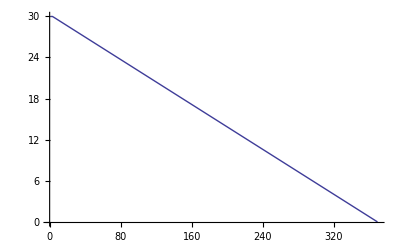

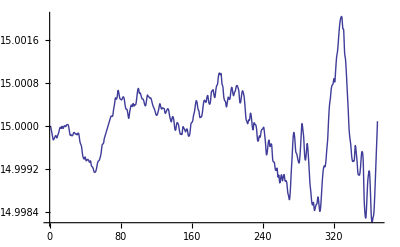

```mathematica
(*draw*)
φ1f=Interpolation[φ1];
φ2f=Interpolation[φ2];
plot1=Plot[φ1f[x],{x,1,i}, PlotRange->All]
plot2=Plot[φ2f[x],{x,1,i},PlotRange->All]
```